```mathematica
V= 10
h1=1
h2=10
h3 = 0.1
```

10

1

10

0.1

```mathematica
rce1 = {x'[t]==V*Cos[β[t]]-(V/h1)y[t],y'[t]==V*Sin[β[t]],β'[t]==(V/h1)(Cos[β[t]])^2}
rce2 = {x'[t]==V*Cos[β[t]]-(V/h2)y[t],y'[t]==V*Sin[β[t]],β'[t]==(V/h2)(Cos[β[t]])^2}
rce3 = {x'[t]==V*Cos[β[t]]-(V/h3)y[t],y'[t]==V*Sin[β[t]],β'[t]==(V/h3)(Cos[β[t]])^2}
```

{x'[t]==10 Cos[β[t]]-10 y[t],y'[t]==10 Sin[β[t]],β'[t]==10 Cos[β[t]]^2}

{x'[t]==10 Cos[β[t]]-y[t],y'[t]==10 Sin[β[t]],β'[t]==Cos[β[t]]^2}

{x'[t]==10 Cos[β[t]]-100. y[t],y'[t]==10 Sin[β[t]],β'[t]==100. Cos[β[t]]^2}

```mathematica
sol11 = NDSolve[Join[rce1,{x[0]==1,y[0]==0,β[0]==2.6924934515066306}],{x,y,β},{t,0,3600}]
sol21 = NDSolve[Join[rce2,{x[0]==1,y[0]==0,β[0]==3.0916550055755416}],{x,y,β},{t,0,3600}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

```mathematica
sol31  = NDSolve[Join[rce3,{x[0]==1,y[0]==0,β[0]==1.9153177950415883}],{x,y,β},{t,0,3600}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

```mathematica
sol12 =NDSolve[Join[rce1,{x[0]==5,y[0]==0,β[0]==2.081180495890659}],{x,y,β},{t,0,3600}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

```mathematica
sol22 = NDSolve[Join[rce2,{x[0]==5,y[0]==0,β[0]==2.8989720588197256}],{x,y,β},{t,0,3600}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

```mathematica
sol32 = NDSolve[Join[rce3,{x[0]==5,y[0]==0,β[0]==1.715821888903854}],{x,y,β},{t,0,3600}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

```mathematica
sol13= NDSolve[Join[rce1,{x[0]==-5,y[0]==0,β[0]==5.222773149480452}],{x,y,β},{t,0,3600}]
sol23= NDSolve[Join[rce2,{x[0]==-5,y[0]==0,β[0]==6.040564712409519}],{x,y,β},{t,0,3600}]
sol33= NDSolve[Join[rce3,{x[0]==-5,y[0]==0,β[0]==4.85741454249365}],{x,y,β},{t,0,3600}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

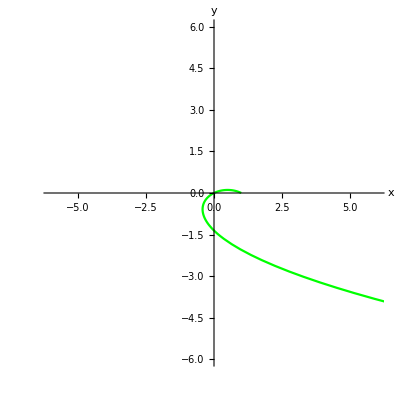

```mathematica
graf11  =ParametricPlot[Table[{x[t],y[t]}/.sol11],{t,0,1},AxesLabel->{x,y},PlotRange->{{-6,6},{-6,6}},PlotStyle->{Green}]
```

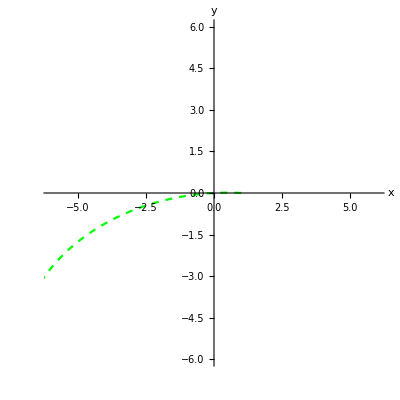

```mathematica
graf21  =ParametricPlot[Table[{x[t],y[t]}/.sol21],{t,0,1},AxesLabel->{x,y},PlotRange->{{-6,6},{-6,6}},PlotStyle->{Green,Dashed}]
```

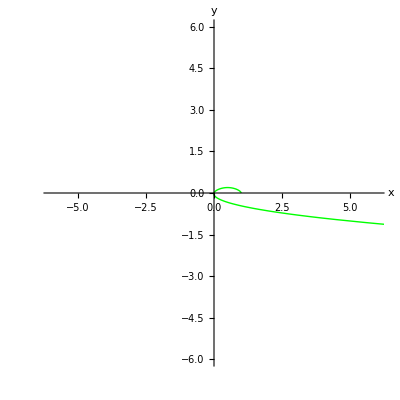

```mathematica
graf31  =ParametricPlot[Table[{x[t],y[t]}/.sol31],{t,0,1},AxesLabel->{x,y},PlotRange->{{-6,6},{-6,6}},PlotStyle->{Green,Thick,Thick}]
```

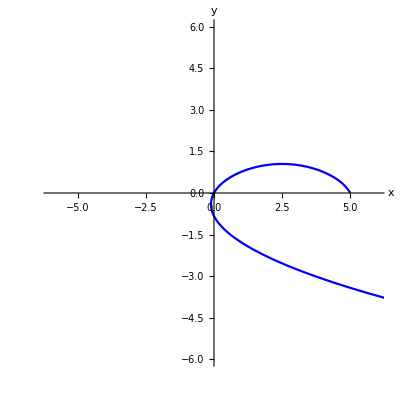

```mathematica
graf12  =ParametricPlot[Table[{x[t],y[t]}/.sol12],{t,0,1},AxesLabel->{x,y},PlotRange->{{-6,6},{-6,6}},PlotStyle->{Blue}]
```

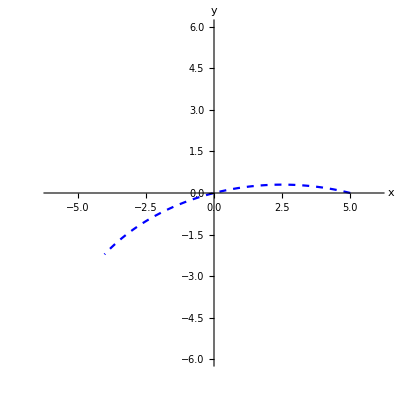

```mathematica
graf22  =ParametricPlot[Table[{x[t],y[t]}/.sol22],{t,0,1},AxesLabel->{x,y},PlotRange->{{-6,6},{-6,6}},PlotStyle->{Blue,Dashed}]
```

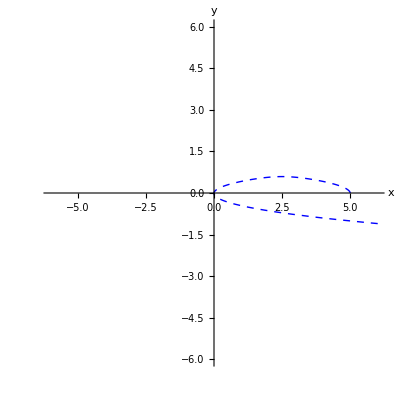

```mathematica
graf32  =ParametricPlot[Table[{x[t],y[t]}/.sol32],{t,0,1},AxesLabel->{x,y},PlotRange->{{-6,6},{-6,6}},PlotStyle->{Blue,Dashed,Thick}]
```

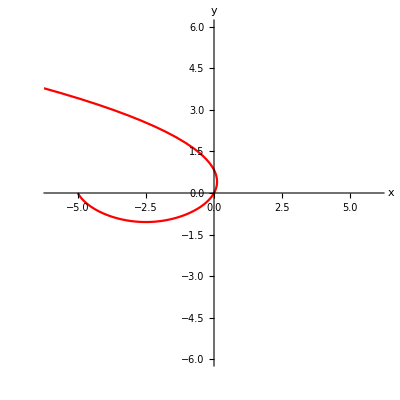

```mathematica
graf13  =ParametricPlot[Table[{x[t],y[t]}/.sol13],{t,0,1},AxesLabel->{x,y},PlotRange->{{-6,6},{-6,6}},PlotStyle->{Red}]
```

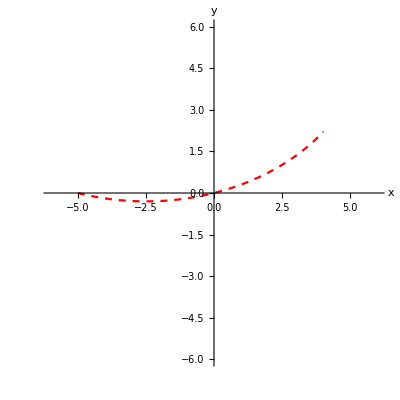

```mathematica
graf23  =ParametricPlot[Table[{x[t],y[t]}/.sol23],{t,0,1},AxesLabel->{x,y},PlotRange->{{-6,6},{-6,6}},PlotStyle->{Red,Dashed}]
```

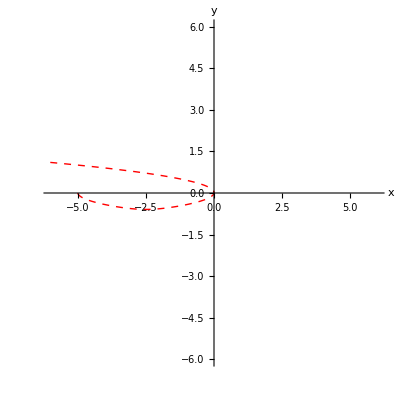

```mathematica
graf33  =ParametricPlot[Table[{x[t],y[t]}/.sol33],{t,0,1},AxesLabel->{x,y},PlotRange->{{-6,6},{-6,6}},PlotStyle->{Red,Dashed,Thick}]
```

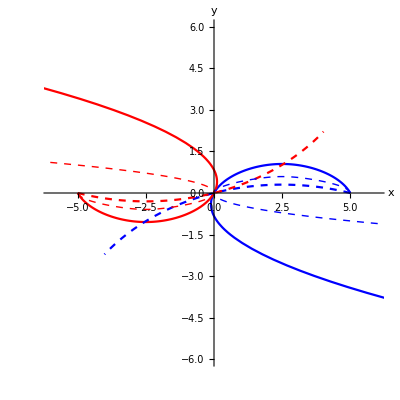

```mathematica
Show[graf12,graf13,graf22,graf23,graf32,graf33]
```

```mathematica
t11=0.09638891129126581
t21=0.0999584008892277
t31=0.05573634242004828
t12=0.35723012793161646
t22=0.4949920477330314
t32=0.13693852738739534
t13=0.35723012793161657
t23=0.49499204773302974
t33=0.13693852738739606
```

0.0963889

0.0999584

0.0557363

0.35723

0.494992

0.136939

0.35723

0.494992

0.136939

```mathematica
Tabulka0 = Table[{{1,0},{5,0},{-5,0}}]
```

{{1,0},{5,0},{-5,0}}

```mathematica
Tabulka1 = Table[{t11,t12,t13}]
```

{0.0963889,0.35723,0.35723}

```mathematica
Tabulka2 = Table[{t21,t22,t23}]
```

{0.0999584,0.494992,0.494992}

```mathematica
Tabulka3 = Table[{t31,t32,t33}]
```

{0.0557363,0.136939,0.136939}

```mathematica
NumberForm[Grid[{{"Start X/Y","h = 1","h = 10","h = 0.1"},{TableForm[Tabulka0],TableForm[Tabulka1],TableForm[Tabulka2],TableForm[Tabulka3]}},Frame->All],7]
```

Start X/Y | h = 1 | h = 10 | h = 0.1
1 | 0
5 | 0
-5 | 0 | 0.09638891
0.3572301
0.3572301 | 0.0999584
0.494992
0.494992 | 0.05573634
0.1369385
0.1369385

```mathematica
Tabulka11=Table[{β[0]/.sol11,β[0]/.sol12,β[0]/.sol13}]
```

{{2.69249},{2.08118},{5.22277}}

```mathematica
Tabulka22=Table[{β[0]/.sol21,β[0]/.sol22,β[0]/.sol23}]
```

{{3.09166},{2.89897},{6.04056}}

```mathematica
Tabulka33=Table[{β[0]/.sol31,β[0]/.sol32,β[0]/.sol33}]
```

{{1.91532},{1.71582},{4.85741}}

```mathematica
NumberForm[Grid[{{"Start X/Y","h = 1","h = 10","h = 0.1"},{TableForm[Tabulka0],TableForm[Tabulka11],TableForm[Tabulka22],TableForm[Tabulka33]}},Frame->All],7]
```

Start X/Y | h = 1 | h = 10 | h = 0.1
1 | 0
5 | 0
-5 | 0 | 2.692493
2.08118
5.222773 | 3.091655
2.898972
6.040565 | 1.915318
1.715822
4.857415